# EGGS - Barium Effective Hamiltonian Last Updated: 08/30/2022

```mathematica
Quit[]
```

```mathematica
Remove["Global`*"];ClearInOut[];
```

```mathematica
(*todo: create vector/ket/basis object and modify operators on it*)
(*todo: generalize by specifying angular momentum objects and total angular momentum objects and have users specify and generate on the fly*)
(*todo: using mat.unitvector is unreasonable*)
(*todo: create general restrict function that pumps out restriction matrices*)
```

```mathematica
(*todo: fix problem where complexexpand isn't hitting sparsearray*)
```

## Prep

## Useful Stuff

### Setup

```mathematica
(*turn off messages*)
ParallelEvaluate[
Off[General::munfl];
Off[LaunchKernels::nodef];
Off[InterpolatingFunction::dmval];];
```

```mathematica
(*turn off wigner n-j and clebsch-gordan error messages*)
Off[SixJSymbol::tri];Off[ClebschGordan::tri];Off[ClebschGordan::phy];
```

```mathematica
(*import packages*)
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
Needs["Utilities`CleanSlate`"]
```

### Functions

```mathematica
(*memory*)
memory:=Row[{"Memory Used: ",MemoryInUse[]/1024^2.," MB"}];
```

```mathematica
(*load data back in*)
loadholders[filename_,holder_]:=Module[{res},
<<(ToString[filename]);
res=GetFidelity[holder,tsweepmax];
Clear[holder];
res]
```

## Constants

### Fundamental

```mathematica
ℏ=1.0545718*^-34;c=2.99792458*^8;kb=1.38064852*^-23;
```

```mathematica
me=9.10938356*^-31;qe=1.60217662*^-19;ϵ0 = 8.8541878128*^-12;
```

```mathematica
μB=(qe*ℏ)/(2*me);gS=2;gL=1;
```

### Derived

```mathematica
ke2=2.30707751*^-28;α=ke2/(ℏ*c);a0=ℏ^2/(me*ke2);
```

### Defined

```mathematica
debye=1.*^-21/c;amu=1.66053904*^-27;
```

### Frequency

```mathematica
thz=1.*^12;ghz=1.*^9;mhz=1.*^6;khz=1.*^3;
wthz=π*2.*^12;wghz=π 2.*^9;wmhz=π 2.*^6;wkhz=π 2.*^3;
```

### Time

```mathematica
ms=1.*^-3;μs=1.*^-6;ns=1.*^-9;
```

### Distance

```mathematica
mm=1.*^-3;μm=1.*^-6;nm=1.*^-9;
```

## Functions

### Transforms & Diff Eqs

```mathematica
(*transforms a Hamiltonian to the interaction picture with respect to U*)
ToIntPic[H_,U_]:=With[
{Udag=ComplexExpand[ConjugateTranspose[Normal[U]]]//SparseArray},
Return[Udag.H.U]
];
```

```mathematica
SolveSchrodinger[H_,initialstate_,t1_,t2_]:=Dispatch[First@NDSolve[#,
Basisψ,
{t,t1,t2},
MaxSteps->∞,
Method->{"StiffnessSwitching",Method->{Automatic,Automatic},"EquationSimplification"->"Solve"}]]&[
Join[
Thread[(Basisψ/.{t->t1})==initialstate],
Thread[BasisψDiff+ⅈ/ℏ*(#)==0]&[H.Basisψ]
]];
```

```mathematica
Commutator[mat1_,mat2_]:=mat1.mat2-mat2.mat1;
```

### Getting & Processing Data

```mathematica
(*formats the solveschrodinger return object into interpolating functions organized by state*)
GetPops[soln_]:=Basisψ/.soln;
```

```mathematica
(*get numerical values from a list of interpolating function objects*)
GetPoints[func_,t1_,t2_,numPoints_:300]:=Module[
{func2,
tArr=Range[t1,t2,(t2-t1)/(numPoints)]},
func2[tDJ_]:=Evaluate[func/.{t->tDJ}];
Thread[func2[tArr]]
]
```

```mathematica
(*combines GetPops and GetPoints appropriately*)
GetPopsPoints[soln_,t1_,t2_,numPoints_:300]:=Module[
{func2=Basisψ/.soln,
tArr=Range[t1,t2,(t2-t1)/(numPoints)]},
func2[tDJ_]:=Evaluate[func/.{t->tDJ}];
Thread[func2[tArr]]
]
```

### Effective Hamiltonian Method (James & Jerke)

```mathematica
(*calculates the James & Jerke effective Hamiltonian from an interaction picture Hamiltonian*)
Heff[Ham_]:=Module[
{arrayrules=Expand[ArrayRules[SparseArray[Ham]][[;;-2]]],
arraydim=Dimensions[Ham],
ind, expr, vals, 
coefficientsArr,exponentsArr,uniqueExponents,coefficientsArrPositions,
hcoeffArr,hcoeffPos,hMatArr,hMatArr2},
(*split index from values and get each element of sum separately*)
ind=arrayrules[[;;,1]];expr=arrayrules[[;;,2]]/.{x_+0.:>x};vals=List@@@expr;
(*separate coefficients from exponent*)
coefficientsArr=vals/.{x_*ⅇ^(__):>x};
exponentsArr=Exponent[#,ⅇ]&/@vals;
(*then strip zeros and t from exponent*)
exponentsArr=Im[ComplexExpand[exponentsArr]/.{t->1}];
(*make exponent same precision as later exp*)
exponentsArr=SetPrecision[exponentsArr,9];
(*get unique exponents*)
uniqueExponents=DeleteDuplicates[Abs[Flatten[exponentsArr]]]//Sort;
(*remove any pesky zeros from the list*)
uniqueExponents=DeleteCases[uniqueExponents,0];
(*get coefficient positions for each unique exponent*)
coefficientsArrPositions=Position[exponentsArr,#]&/@uniqueExponents;
(*get coefficients*)
hcoeffArr=Apply[coefficientsArr[[##]]&,coefficientsArrPositions,{2}];
(*get positions*)
hcoeffPos=ind[[#,;;]]&/@coefficientsArrPositions[[;;,;;,1]];
(*create matrix for each unique exponent*)
hMatArr=MapThread[SparseArray[#1->#2,arraydim]&,{hcoeffPos,hcoeffArr}];
Return[AssociationThread[uniqueExponents->hMatArr]]
];
```

```mathematica
(*gives the zeroth-order effective Hamiltonian using the result of Heff*)
Heff0[Heff_]:=Module[
{wm=Keys[Heff],
hm=Values[Heff]},
Total[(1/(ℏ*wm))*(Commutator[ConjugateTranspose[#],#]&/@hm)]
];
```

```mathematica
(*gives the higher-order effective Hamiltonian using the result of Heff*)
HeffEx[Heff1_]:=Module[
{Hmn,Hres,
ind=Tuples[{#,#}]&[Range[Length[Heff1]]],
wm=Keys[Heff1],
hm=Values[Heff1]},
Hmn[i_,j_]:=1/(2ℏ)(1/wm[[i]]+1/wm[[j]])*Commutator[ConjugateTranspose[hm[[i]]],hm[[j]]]*Exp[ⅈ*(wm[[i]]-wm[[j]])*t];
Plus@@(Hmn@@@ind)
]
```

### RWA

```mathematica
(*removes any terms with frequency beyond a cutoff and recreate the original matrix*)
HRWA[Heff_]:=Module[
{wm=Keys[Heff],
hm=Values[Heff]},
(*todo: remove terms wm>cutoff*)
Total[(1/(ℏ*wm))*(Commutator[ConjugateTranspose[#],#]&/@hm)]
];
```

## Configuration

-Graphics-

## Atom Configuration

### States

```mathematica
(*L: total orbital angular momentum*)
L={0,1,2};
```

```mathematica
(*S: total spin angular momentum*)
S=1/2;
```

```mathematica
(*K: nuclear angular momentum*)
K=1/2;
```

### Transition Elements

```mathematica
(*transition dipole moments*)
d493=2.01743*^-29;
d455=2.81729*^-29;
d585=5.722101*^-30;
d614=1.43425*^-29;
d650=1.22799*^-29;
```

```mathematica
(*
transition dipole elements
these are written in the form: {{L1,J1},{L2,J2}} -> dipoleMoment
*)
transitionDipoleMoments=<|
{{0,1/2},{1,1/2}}->d493,
{{0,1/2},{1,3/2}}->d455,
{{1,1/2},{2,3/2}}->d650,
{{1,3/2},{2,5/2}}->d614
|>;
```

### Zeeman

```mathematica
(*nuclear magnetic moment*)
gK=0;
```

## Laser Power

```mathematica
(*laser beam waist*)
w0=20*μm;
```

```mathematica
(*laser beam power*)
P0=1;
```

```mathematica
(*calculate electric field*)
Efield = √((2 P0)/(π w0^2 c ϵ0));
```

## Transition Frequencies

```mathematica
(*fine structure shifts*)
Δ1 =  9.925*wghz;
Δ2 = 1.840*wghz;
Δ3 = 0.940*wghz;
Δ4 = 0.625*wghz;
Δ5 = 0.08967*wghz;
```

```mathematica
(*493nm*)
f532 = c/(532*^-9);ω532 = 2π f532;
ω493 = (2π c)/( 493.4077*^-9);Δ493 = ω532-ω493;
Δ493f10 = ω532-(ω493);
Δ493f11 = ω532-(ω493 - Δ2) ;
Δ493f01 = ω532-(ω493 - Δ2 -Δ1);
```

```mathematica
(*455nm*)
f455 =c/(455*^-9);ω455 = 2π f455;Δ455 = ω532-ω455;
Δ455f12 = ω532-(ω455);
Δ455f11 = ω532-(ω455 + Δ4);
Δ455f01 = ω532-(ω455 + Δ4 - Δ1);
```

```mathematica
(*614nm & 650nm*)
f614=c/(614*^-9);ω614 = 2π f614;
Δ614 = ω532-ω614;
ω650 =  2π( 461.312*^12);
```

## Energies

```mathematica
(*set energies of the different states*)
EArr={Δ1,0,ω493,ω493-Δ2,ω455+Δ4,ω455,ω493-ω650,ω493-ω650-Δ3,ω455-ω614,ω455-ω614+Δ5};
(*set degeneracies of each state*)
rptArr={1,3,1,3,3,5,3,5,5,7};
```

```mathematica
(*create list of energies for each state*)
E0=MapThread[ConstantArray,{EArr,rptArr}]//Flatten;
```

## Create Infrastructure

## Bases

### Fine Structure

```mathematica
(*create the rest of the fine structure quantum numbers*)
J=Range[Abs[#-S],Abs[#+S]]&/@L;
MJ=Range[-#,#]&/@J;
LJ=Flatten[Tuples[{{L[[#]]},J[[#]]}]&/@Range[Length[L]],1];
```

### Hyperfine Structure

```mathematica
(*create the rest of the hyperfine structure quantum numbers*)
F=Range[Abs[K-#],Abs[K+#]]&/@LJ[[;;,2]];
LJF=Flatten[Tuples[{{LJ[[#,1]]},{LJ[[#,2]]},F[[#]]}]&/@Range[Length[F]],1];
```

### Motional States

### Total Basis

```mathematica
(*combine the constituent bases into a single vector*)
BasisHF=Flatten[(Flatten/@Tuples[{{#},Range[-#[[3]],#[[3]]]}])&/@LJF,1];
```

```mathematica
(*create a vector to hold the displayable names of each state*)
BasisHFDisplay={(Subscript@@#/.{0->"S",1->"P",2->"D"})&/@BasisHF[[;;,;;2]],Ket/@(MapThread[StringJoin["F=",ToString[#1],", M_F=",ToString[#2]]&,Transpose[BasisHF[[;;,3;;]]]])}//Transpose;
```

```mathematica
(*create basis for time-dependent, just in case*)
numStates=Length[BasisHF];
Basisψ=StringInsert["ψ[t]",ToString[#],2]&/@Range[numStates];
BasisψDiff=ToExpression[StringInsert[#,"'",-4]&/@Basisψ];
Basisψ=ToExpression[Basisψ];
```

### Zeeman

```mathematica
(*good quantum number*)
LJK=Flatten/@Tuples[{LJ,{K}}];
```

```mathematica
(*create structure bases for zeeman: L, J, K, Subscript[M, J], Subscript[M, K]*)
BasisZeeman=Flatten[(Flatten/@Tuples[{{#},Range[-#[[2]],#[[2]],1],Range[-#[[3]],#[[3]],1]}])&/@LJK,1];
```

```mathematica
(*display *)
BasisZeemanDisplay={(Subscript@@#/.{0->"S",1->"P",2->"D"})&/@BasisZeeman[[;;,;;2]],Ket/@(MapThread[StringJoin["M_J=",ToString[#1],", M_K=",ToString[#2]]&,Transpose[BasisZeeman[[;;,4;;]]//N]])}//Transpose;
```

## Operators

### Total Momentum Operators

These operators are used to enforce manage transitions between angular momentum states.
The value after the first letter indicates the transition supported.
	0 indicates transitions to the same total momentum state (e.g. ΔJ=0).
	p (plus) indicates transitions that raise the total momentum (e.g. ΔF = +1).
	m (minus) indicates transitions that lower the total momentum (e.g. ΔF = -1).
	x is the Pauli-x operator for that quantum number (i.e. supports ΔJ=±1 transitions).

```mathematica
(*orbital angular momentum operator*)
L0=SparseArray[Outer[KroneckerDelta,#,#]&[BasisHF[[;;,1]]]];
L0-=KroneckerProduct[#,#]&[KroneckerDelta[0,#]&/@BasisHF[[;;,1]]];
```

```mathematica
Lp=Outer[KroneckerDelta,#-1,#]&[BasisHF[[;;,1]]];
Lp=SparseArray[Lp];Lm=Transpose[Lp];
Lx=Lp+Lm;
```

```mathematica
(*total angular momentum operator*)
J0=Outer[KroneckerDelta,#,#]&[BasisHF[[;;,2]]];
J0-=KroneckerProduct[#,#]&[KroneckerDelta[0,#]&/@BasisHF[[;;,2]]];
```

```mathematica
Jp=Outer[KroneckerDelta,#-1,#]&[BasisHF[[;;,2]]];
Jp=SparseArray[Jp];Jm=Transpose[Jp];
Jx=Jp+Jm;
```

```mathematica
(*total atomic and nuclear angular momentum operator*)
F0=Outer[KroneckerDelta,#,#]&[BasisHF[[;;,3]]];
F0-=KroneckerProduct[#,#]&[KroneckerDelta[0,#]&/@BasisHF[[;;,3]]];
```

```mathematica
Fp=Outer[KroneckerDelta,#-1,#]&[BasisHF[[;;,3]]];
Fp=SparseArray[Fp];Fm=Transpose[Fp];
Fx=Fp+Fm;
```

### Angular Momentum Projection Operators

```mathematica
(*todo: fix*)
```

```mathematica
σp=Outer[KroneckerDelta,#-1,#]&[BasisHF[[;;,4]]];
σp=SparseArray[σp];σm=Transpose[σp];
σx=σp+σm;
```

```mathematica
π0=SparseArray[Outer[KroneckerDelta,#,#]&[BasisHF[[;;,4]]]];
```

### Wigner-Eckart (Explanation)

-Graphics-
-Graphics-

FFcoefficients (matrix): the coefficient terms and the 6-j symbols (i.e. (-1)^(F'-F+m'_F-m_F)√((2F+1)/(2F'+1)))
FF6 (matrix): 
FFm (matrix): the Clebsch-Gordan coefficients for transitions with Δm_F=-1

FFp (matrix): the Clebsch-Gordan coefficients for transitions with Δm_F=+1

FF0 (matrix): the Clebsch-Gordan coefficients for transitions into the same m_F state/

### Wigner-Eckart (Calculation)

```mathematica
(*calculate transition coefficients*)
FFcoefficients=Outer[SixJSymbol[{#2[[2]],#1[[2]],1},{#1[[3]],#2[[3]],K}]*√((2*#1[[2]]+1)*(2*#1[[3]]+1))*(-1)^(#1[[2]]+1+K-#1[[3]]+#2[[4]]-#1[[4]])&,BasisHF,BasisHF,1]//SparseArray;
```

```mathematica
(*calculate clebsch-gordan coefficients*)
FFm=Outer[ClebschGordan[{#1[[3]],#1[[4]]},{1,1},{#2[[3]],#2[[4]]}]&,BasisHF,BasisHF,1]//SparseArray;
FFp=Outer[ClebschGordan[{#1[[3]],#1[[4]]},{1,-1},{#2[[3]],#2[[4]]}]&,BasisHF,BasisHF,1]//SparseArray;
FF0=Outer[ClebschGordan[{#1[[3]],#1[[4]]},{1,0},{#2[[3]],#2[[4]]}]&,BasisHF,BasisHF,1]//SparseArray;
```

```mathematica
(*create matrices to select different dipole transitions*)
transitionMatrixL[LJstate1_,LJstate2_]:=Outer[
KroneckerDelta[LJstate1[[1]],#1[[1]]]*KroneckerDelta[LJstate2[[1]],#2[[1]]]*KroneckerDelta[LJstate1[[2]],#1[[2]]]*KroneckerDelta[LJstate2[[2]],#2[[2]]]&,
BasisHF[[;;,;;2]],BasisHF[[;;,;;2]],
1]//SparseArray;
transitionMatrices=Values[transitionDipoleMoments].(transitionMatrixL@@@Keys[transitionDipoleMoments]);
transitionMatrices+=Transpose[transitionMatrices];
```

### Electric Dipole (E1) Transitions

```mathematica
Mxp=FFcoefficients*Lx*FFp*σp;
Mxm=FFcoefficients*Lx*FFm*σm;
Mx0=FFcoefficients*Lx*FF0*π0;
Mxx=Mxm+Mxp;
```

### Magnetic Dipole (M1) Transitions

```mathematica
(*M1 hyperfine transitions require ΔF=0, ±1, and Subscript[ΔM, F]=0, ±1*)
```

```mathematica
(*the M1x0 operator addresses Subscript[ΔM, F]=0 transitions; we use it to prevent the forbidden ΔF=0 Subscript[M, F]=0 -> Subscript[M, F]=0 transition*)
M1x0=KroneckerProduct[#,#]&[KroneckerDelta[0,#]&/@BasisHF[[;;,4]]];
M1x=L0*J0*((Fx+F0)*(σx+π0)-F0*M1x0);
```

### Restrictions

```mathematica
(*enforce ΔL=0 condition*)
ΔL0=SparseArray[Outer[KroneckerDelta,#,#]&[BasisHF[[;;,1]]]];
```

```mathematica
(*enforce ΔJ=0 condition*)
ΔJ0=Outer[KroneckerDelta,#,#]&[BasisHF[[;;,2]]];
```

## Testing

```mathematica
(*todo: using mat.unitvector is unreasonable*)
```

```mathematica
(*shows the resultant states after an operator acts on an initial state, ignoring coefficients*)
TestMatrix[mat_,ind_]:=TableForm[
#,
TableHeadings->{{BasisHFDisplay[[ind]]},None}
]&[
BasisHFDisplay[[SparseArray[mat.UnitVector[36,ind]]["NonzeroPositions"]//Flatten]]
];
```

```mathematica
(*same as testmatrix but shows coefficients as well*)
TestMatrix2[mat_,ind_]:=TableForm[
Transpose[Join[{Values[#]},Transpose[BasisHFDisplay[[Keys[#]//Flatten]]]]],
TableHeadings->{{BasisHFDisplay[[ind]]},{"Coefficient","Fine State","Hyperfine State"}}
]&[
ArrayRules[SparseArray[mat.UnitVector[36,ind]]][[;;-2]]
]
```

```mathematica
(**)
(*StateToVector[state_]:=*)
```

```mathematica
(*same as testmatrix but shows coefficients as well*)
TestMatrixZeeman[mat_,ind_]:=TableForm[
Transpose[Join[{Values[#]},Transpose[BasisZeemanDisplay[[Keys[#]//Flatten]]]]],
TableHeadings->{{BasisHFDisplay[[ind]]},{"Coefficient","Fine State","Hyperfine State"}}
]&[
ArrayRules[SparseArray[mat.UnitVector[36,ind]]][[;;-2]]
]
```

## Zeeman

```mathematica
(*landé g-factor for J*)
gJ[L_,J_,S_:S] := (3J(J+1)+S(S+1)-L(L+1))/(2J (J+1));
```

```mathematica
(*landé g-factor for F*)
gF[L_,J_,F_,S_:S,I_:K]:= gJ[J,L,S] (F(F+1) - I(I+1) + J(J+1))/(2F(F+1));
```

```mathematica
(*transform HF basis to zeeman*)
BasisTransformHFtoZeeman=Outer[ClebschGordan[#1[[{2,4}]],#1[[{3,5}]],#2[[3;;4]]]&,BasisZeeman,BasisHF,1]//SparseArray;
BasisTransformHFtoZeeman*=(ΔL0*ΔJ0);
```

```mathematica
(*create stuff for HZeemanLJ in advance*)
gJArr=gJ@@@BasisZeeman[[;;,1;;2]];
mJz=BasisZeeman[[;;,4]];
mKz=BasisZeeman[[;;,5]];
```

```mathematica
HZeemanLJ[Bz_]:=Transpose[BasisTransformHFtoZeeman].SparseArray[{Band[{1,1}]->#}].BasisTransformHFtoZeeman&[
μB*Bz*(gJArr*mJz+gK*mKz)
]//SparseArray;
```

```mathematica
BDJ=5*^-4;
HamZeeman=HZeemanLJ[BDJ];
HamZeeman=Chop[HamZeeman,1*^-30];
```

```mathematica
HZe:=H0+HamZeeman/ℏ;
```

```mathematica
UZe:=MatrixExp[-ⅈ*t*HZe];
```

## Base Hamiltonians

```mathematica
(*create internal energy hamiltonian*)
H0:=DiagonalMatrix[E0]//SparseArray;
```

```mathematica
(*time-evolution operator for Subscript[H, 0], the internal energy states*)
U0:=SparseArray[{Band[{1,1}]->Exp[-ⅈ*t*E0]}];
```

## Actual Hamiltonians

```mathematica
(*straightforward rabi-flopping hamiltonian*)
HamBar[ω_,Ω_,pol_]:=Ω/2*(Exp[ⅈ*ω*t]+Exp[-ⅈ*ω*t])*({Mxm,Mx0,Mxp,Mxx}[[pol]]);
```

```mathematica
(*magnetic dipole transition*)
HamMag[ω_,Ω_]:=Ω/2*(Exp[ⅈ*ω*t]+Exp[-ⅈ*ω*t])*(M1x);
```

## Calculate Effective Hamiltonian (Basic)

## Generating Effective Hamiltonians

```mathematica
(*get rabi frequencies*)
Ω455=Efield*d455;δ455=10*wkhz;
Ω493=Efield*d493;δ493=10*wkhz;
Ω585=Efield*d585;δ585=10*wkhz;
Ω614=Efield*d614;δ614=10*wkhz;
```

```mathematica
(*generate individual laser hamiltonians*)
HDJ455=HamBar[ω455+δ455,Ω455,1];
HDJ493=HamBar[ω493+δ493,Ω493,4];
HDJ614=HamBar[ω614+δ614,Ω614,4];
```

## Calculate Effective Hamiltonian

```mathematica
(*select hamiltonian*)
hma=SparseArray[{{10,21}->-1/(2 √5),{21,10}->-1/(2 √5)},{36,36}];
HDJ=Ω585/2*(Exp[ⅈ*ω532*t]+Exp[-ⅈ*ω532*t])*hma//FullSimplify;
HDJ=HDJ455;
```

```mathematica
(*take to interaction picture*)
AbsoluteTiming[
HDJint=ToIntPic[HDJ,U0]//TrigToExp;
]
(*get laser frequencies*)
HDJfreqs=ToString/@(c*2*π/Keys[Heff[HDJ]]/nm//Sort);
```

{0.104504,Null}

```mathematica
(*calculate stark shifts*)
AbsoluteTiming[
HeffDJ=Heff[HDJint];
HeffSS=Heff0[HeffDJ];
]
```

{0.045906,Null}

## Diagonalizing Zeroth-Order Effective Hamiltonian

```mathematica
(*get rid of pesky imaginary values that arise due to finite precision*)
HeffSS=Re[HeffSS];
```

```mathematica
(*get eigen*)
{HeffEigenval,HeffEigenvec}=Eigensystem[HeffSS];
HeffEigenval/=(ℏ*wkhz);
```

```mathematica
(*remove negligible eigenvalues*)
(*todo: allow customizable cutoff*)
δss=Max[HeffEigenval]*1*^-6;
HeffEigenval=Chop[HeffEigenval,δss];
```

```mathematica
(*remove negligible eigenvector component values*)
δEigenvec=Mean[Max/@HeffEigenvec]*1*^-6;
HeffEigenvec=Chop[HeffEigenvec,δEigenvec];
```

## Process Results

```mathematica
(*get nonzero eigenvalues*)
{nonzeroIndices,nonzeroEigenvalues}={Flatten[Keys[#]],Values[#]}&[ArrayRules[HeffEigenval][[;;-2]]];
(*get nonzero eigenvectors*)
nonzeroEigenvectors=HeffEigenvec[[#]]&/@nonzeroIndices;
```

```mathematica
(*separate eigenvector indices and values*)
separatedEigenvectors=(ArrayRules[#][[;;-2]])&/@nonzeroEigenvectors;
{stateIndices,stateCoefficients}=Transpose[{Flatten[Keys[#]],Values[#]}&/@separatedEigenvectors];
```

```mathematica
(*format new eigenstates*)
eigenstateDisplay=BasisHFDisplay[[#]]&/@stateIndices;
eigenbasisTable=Transpose[Append[Transpose[eigenstateDisplay[[#]]],stateCoefficients[[#]]]]&/@Range[Length[nonzeroIndices]];
eigenbasisTable=TableForm[#,TableHeadings->{None,{"Fine","Hyperfine","Coefficient"}}]&/@eigenbasisTable;
```

```mathematica
(*format*)
resultsTitle="Laser Wavelengths (nm): "<>StringRiffle[HDJfreqs,", "];
formattedDisplay=
Labeled[
TableForm[
Transpose[{nonzeroEigenvalues,eigenbasisTable}],
TableHeadings->{None,{"Stark Shift (x2π kHz)","Eigenbasis"}},
TableAlignments->Center
],
resultsTitle,Top,Frame->True
];
```

### Results

```mathematica
formattedDisplay
```

Stark Shift (x2π kHz) | Eigenbasis
1.35491×10^13 | Fine | Hyperfine | Coefficient
P_(3/2) | F=2, M_F=2 | 1.
-1.3549×10^13 | Fine | Hyperfine | Coefficient
S_(1/2) | F=1, M_F=1 | 1.
6.77455×10^12 | Fine | Hyperfine | Coefficient
P_(3/2) | F=2, M_F=1 | 1.
-6.77448×10^12 | Fine | Hyperfine | Coefficient
S_(1/2) | F=1, M_F=0 | 1.
-2.25818×10^12 | Fine | Hyperfine | Coefficient
S_(1/2) | F=1, M_F=-1 | 1.
2.25818×10^12 | Fine | Hyperfine | Coefficient
P_(3/2) | F=2, M_F=0 | 1.
-7.22619×10^7 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=-1 | 1.
-7.22619×10^7 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=0 | 1.Laser Wavelengths (nm): 455.

## Get Stark Shifts vs B-Field

```mathematica
(*set b-field values*)
BArr={5*^-4,1*^-3};
```

```mathematica
(*create zeeman hamiltonians and time evolution propagators*)
AbsoluteTiming[
HZeArr=HZeemanLJ/@BArr;
HZeArr=Chop[HZeArr,1*^-30]/ℏ;
UZeArr=ParallelMap[MatrixExp[-ⅈ*t*(H0+#)]&,HZeArr];
]
```

{0.141806,Null}

```mathematica
(*transform into interaction picture and take effective hamiltonian*)
AbsoluteTiming[
HintArr=ParallelMap[TrigToExp[ToIntPic[HDJ,#]]&,UZeArr];
]
```

{3.40683,Null}

```mathematica
(*take effective hamiltonian*)
AbsoluteTiming[
HeffArr=Heff/@HintArr;
HeffSSArr=ParallelMap[Heff0,HeffArr];
]
HeffSSArr=Re[HeffSSArr];
```

{9.71658,Null}

```mathematica
(*diagonalize and remove very small values*)
DiagonalizeHeff[Hmat_]:=Module[
{δEigenval=Max[Hmat]*1*^-6,
eigenval,eigenvec,δEigenvec},
{eigenval,eigenvec}=Eigensystem[Hmat];
eigenval/=(ℏ*wkhz);
eigenval=Chop[eigenval,δEigenval];
δEigenvec=Abs[Mean[Max/@eigenvec]*1*^-6];
eigenvec=Chop[eigenvec,δEigenvec];
Return[{eigenval,eigenvec}];
]
diagonalHeffResArr=DiagonalizeHeff/@HeffSSArr;
```

```mathematica
ProcessHeffArr[eigenval_,eigenvecs_]:=Module[
{nonzeroIndices,nonzeroEigenvalues,nonzeroEigenvectors,separatedEigenvectors,stateIndices,stateCoefficients},
(*get nonzero eigenvalues*)
{nonzeroIndices,nonzeroEigenvalues}={Flatten[Keys[#]],Values[#]}&[ArrayRules[eigenval][[;;-2]]];
(*get nonzero eigenvectors*)
nonzeroEigenvectors=eigenvecs[[#]]&/@nonzeroIndices;
(*separate eigenvector indices and values*)
separatedEigenvectors=(ArrayRules[#][[;;-2]])&/@nonzeroEigenvectors;
{stateIndices,stateCoefficients}=Transpose[{Flatten[Keys[#]],Values[#]}&/@separatedEigenvectors];
(*todo: associate stateindices to coefficients*)
Return[{nonzeroEigenvalues,nonzeroIndices,stateIndices,stateCoefficients}];
]
processedHeffArr=ProcessHeffArr@@@diagonalHeffResArr;
```

```mathematica
ProcessHeffArr2[eigenval_,eigenvecs_]:=Module[
{nonzeroIndices,nonzeroEigenvalues,nonzeroEigenvectors,separatedEigenvectors,stateIndices,stateCoefficients,eigenstateDisplay,eigenbasisTable,formattedDisplay},
(*get nonzero eigenvalues*)
{nonzeroIndices,nonzeroEigenvalues}={Flatten[Keys[#]],Values[#]}&[ArrayRules[eigenval][[;;-2]]];
(*get nonzero eigenvectors*)
nonzeroEigenvectors=eigenvecs[[#]]&/@nonzeroIndices;
(*separate eigenvector indices and values*)
separatedEigenvectors=(ArrayRules[#][[;;-2]])&/@nonzeroEigenvectors;
{stateIndices,stateCoefficients}=Transpose[{Flatten[Keys[#]],Values[#]}&/@separatedEigenvectors];
(*format new eigenstates*)
eigenstateDisplay=BasisHFDisplay[[#]]&/@stateIndices;
eigenbasisTable=Transpose[Append[Transpose[eigenstateDisplay[[#]]],stateCoefficients[[#]]]]&/@Range[Length[nonzeroIndices]];
eigenbasisTable=TableForm[#,TableHeadings->{None,{"Fine","Hyperfine","Coefficient"}}]&/@eigenbasisTable;
(*format*)
formattedDisplay=
Labeled[
TableForm[
Transpose[{nonzeroEigenvalues,eigenbasisTable}],
TableHeadings->{None,{"Stark Shift (x2π kHz)","Eigenbasis"}},
TableAlignments->Center
],
"interesting title",Top,Frame->True
];
Return[formattedDisplay];
]
processedHeffArrDisplays=ProcessHeffArr2@@@diagonalHeffResArr
```

{Stark Shift (x2π kHz) | Eigenbasis
-7.21829×10^7 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=-1 | 0.999979
P_(3/2) | F=2, M_F=-1 | 0.00651279
7.21826×10^7 | Fine | Hyperfine | Coefficient
S_(1/2) | F=0, M_F=0 | 0.0007051
S_(1/2) | F=1, M_F=0 | -1.
7.19868×10^7 | Fine | Hyperfine | Coefficient
S_(1/2) | F=1, M_F=1 | 1.
-7.19852×10^7 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=0 | -0.999972
P_(3/2) | F=2, M_F=0 | -0.00746404
-9.73324×10^6 | Fine | Hyperfine | Coefficient
S_(1/2) | F=0, M_F=0 | 1.
S_(1/2) | F=1, M_F=0 | 0.0007051
9.7324×10^6 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=1 | 0.999979
P_(3/2) | F=2, M_F=1 | 0.00641629
3858.08 | Fine | Hyperfine | Coefficient
P_(1/2) | F=1, M_F=1 | 1.
-3316.62 | Fine | Hyperfine | Coefficient
S_(1/2) | F=1, M_F=-1 | -1.
-3176.39 | Fine | Hyperfine | Coefficient
D_(5/2) | F=3, M_F=-3 | 1.
2873.6 | Fine | Hyperfine | Coefficient
P_(3/2) | F=2, M_F=-2 | 1.
2526.96 | Fine | Hyperfine | Coefficient
P_(1/2) | F=0, M_F=0 | 0.999999
P_(1/2) | F=1, M_F=0 | 0.00126777
2520.12 | Fine | Hyperfine | Coefficient
P_(1/2) | F=0, M_F=0 | -0.00126777
P_(1/2) | F=1, M_F=0 | 0.999999
2450.23 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=-1 | 0.00651279
P_(3/2) | F=2, M_F=-1 | -0.999979
-2112.54 | Fine | Hyperfine | Coefficient
D_(3/2) | F=2, M_F=-2 | 1.
-2085.36 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=-2 | -0.0327979
D_(5/2) | F=3, M_F=-2 | -0.999462
-1920.86 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=-1 | -0.999997
D_(3/2) | F=2, M_F=-1 | -0.00258664
1862.49 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=1 | -0.00641629
P_(3/2) | F=2, M_F=1 | 0.999979
-1544.32 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=-1 | -0.00258664
D_(3/2) | F=2, M_F=-1 | 0.999997
-1497.39 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=-2 | 0.999462
D_(5/2) | F=3, M_F=-2 | -0.0327979
1188.59 | Fine | Hyperfine | Coefficient
P_(1/2) | F=1, M_F=-1 | 1.
-967.276 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=0 | -0.00297788
D_(3/2) | F=2, M_F=0 | 0.999996
-962.654 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=0 | -0.999996
D_(3/2) | F=2, M_F=0 | -0.00297788
841.294 | Fine | Hyperfine | Coefficient
P_(3/2) | F=2, M_F=2 | 1.
-808.346 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=-1 | 0.999088
D_(5/2) | F=3, M_F=-1 | -0.0426942
756.43 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=0 | 0.00746404
P_(3/2) | F=2, M_F=0 | -0.999972
-572.003 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=0 | -0.0466727
D_(5/2) | F=3, M_F=0 | -0.99891
-381.361 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=1 | -0.00257128
D_(3/2) | F=2, M_F=1 | 0.999997
-302.421 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=0 | 0.99891
D_(5/2) | F=3, M_F=0 | -0.0466727
213.48 | Fine | Hyperfine | Coefficient
D_(3/2) | F=2, M_F=2 | 1.
157.482 | Fine | Hyperfine | Coefficient
D_(5/2) | F=3, M_F=3 | 1.
-132.903 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=1 | 0.0454292
D_(5/2) | F=3, M_F=1 | 0.998968
16.8427 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=1 | 0.998968
D_(5/2) | F=3, M_F=1 | -0.0454292
13.8721 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=1 | -0.999997
D_(3/2) | F=2, M_F=1 | -0.00257128
3.35828 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=2 | 0.99931
D_(5/2) | F=3, M_F=2 | -0.037149
-1.7595 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=-1 | -0.0426942
D_(5/2) | F=3, M_F=-1 | -0.999088
0.258574 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=2 | 0.037149
D_(5/2) | F=3, M_F=2 | 0.99931interesting title,Stark Shift (x2π kHz) | Eigenbasis
-7.20768×10^7 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=-1 | 0.999914
P_(3/2) | F=2, M_F=-1 | 0.0131217
7.20766×10^7 | Fine | Hyperfine | Coefficient
S_(1/2) | F=0, M_F=0 | 0.0014102
S_(1/2) | F=1, M_F=0 | -0.999999
7.16963×10^7 | Fine | Hyperfine | Coefficient
S_(1/2) | F=1, M_F=1 | 1.
-7.16948×10^7 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=0 | 0.999889
P_(3/2) | F=2, M_F=0 | 0.0149243
-9.75234×10^6 | Fine | Hyperfine | Coefficient
S_(1/2) | F=0, M_F=0 | 0.999999
S_(1/2) | F=1, M_F=0 | 0.0014102
9.75045×10^6 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=1 | -0.999919
P_(3/2) | F=2, M_F=1 | -0.0127359
3858.08 | Fine | Hyperfine | Coefficient
P_(1/2) | F=1, M_F=1 | 1.
3454.9 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=-1 | -0.0131217
P_(3/2) | F=2, M_F=-1 | 0.999914
-3316.62 | Fine | Hyperfine | Coefficient
S_(1/2) | F=1, M_F=-1 | 1.
-3176.39 | Fine | Hyperfine | Coefficient
D_(5/2) | F=3, M_F=-3 | -1.
-3078.59 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=-2 | -0.0617002
D_(5/2) | F=3, M_F=-2 | -0.998095
2862.48 | Fine | Hyperfine | Coefficient
P_(3/2) | F=2, M_F=-2 | -1.
2753.27 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=1 | -0.0127359
P_(3/2) | F=2, M_F=1 | 0.999919
2530.35 | Fine | Hyperfine | Coefficient
P_(1/2) | F=0, M_F=0 | 0.999997
P_(1/2) | F=1, M_F=0 | 0.00253553
2516.74 | Fine | Hyperfine | Coefficient
P_(1/2) | F=0, M_F=0 | -0.00253553
P_(1/2) | F=1, M_F=0 | 0.999997
-2112.54 | Fine | Hyperfine | Coefficient
D_(3/2) | F=2, M_F=-2 | -1.
-1919.14 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=-1 | 0.999987
D_(3/2) | F=2, M_F=-1 | 0.00518861
-1546.04 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=-1 | -0.00518861
D_(3/2) | F=2, M_F=-1 | 0.999987
-1509.87 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=-2 | 0.998095
D_(5/2) | F=3, M_F=-2 | -0.0617002
1188.59 | Fine | Hyperfine | Coefficient
P_(1/2) | F=1, M_F=-1 | 1.
-969.584 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=0 | 0.00595553
D_(3/2) | F=2, M_F=0 | -0.999982
-960.346 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=0 | 0.999982
D_(3/2) | F=2, M_F=0 | 0.00595553
925.448 | Fine | Hyperfine | Coefficient
P_(3/2) | F=2, M_F=2 | 1.
845.697 | Fine | Hyperfine | Coefficient
P_(3/2) | F=1, M_F=0 | 0.0149243
P_(3/2) | F=2, M_F=0 | -0.999889
-825.785 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=-1 | 0.996611
D_(5/2) | F=3, M_F=-1 | -0.082261
-539.707 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=0 | -0.0924468
D_(5/2) | F=3, M_F=0 | -0.995718
-383.104 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=1 | -0.00512718
D_(3/2) | F=2, M_F=1 | 0.999987
-318.282 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=0 | 0.995718
D_(5/2) | F=3, M_F=0 | -0.0924468
-273.876 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=1 | -0.0929505
D_(5/2) | F=3, M_F=1 | -0.995671
213.48 | Fine | Hyperfine | Coefficient
D_(3/2) | F=2, M_F=2 | 1.
157.482 | Fine | Hyperfine | Coefficient
D_(5/2) | F=3, M_F=3 | 1.
143.023 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=2 | -0.996873
D_(5/2) | F=3, M_F=2 | 0.0790149
15.7931 | Fine | Hyperfine | Coefficient
D_(3/2) | F=1, M_F=1 | 0.999987
D_(3/2) | F=2, M_F=1 | 0.00512718
7.22769 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=1 | -0.995671
D_(5/2) | F=3, M_F=1 | 0.0929505
5.11237 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=-1 | 0.082261
D_(5/2) | F=3, M_F=-1 | 0.996611
1.15135 | Fine | Hyperfine | Coefficient
D_(5/2) | F=2, M_F=2 | 0.0790149
D_(5/2) | F=3, M_F=2 | 0.996873interesting title}

## State Simulation

## First Try

```mathematica
(*create hamiltonian*)
hma=SparseArray[{{10,21}->-1/(2 √5),{21,10}->-1/(2 √5)},{36,36}];
(*HDJ=Ω585/2*(Exp[ⅈ*ω532*t]+Exp[-ⅈ*ω532*t])*hma//FullSimplify;*)
HDJ=HamBar[ω455+δ455,Ω455,1];
HDJ=ToIntPic[HDJ,U0]//TrigToExp;
```

```mathematica
HDJ
```

SparseArray[…]

```mathematica
(*apply RWA*)
HDJeff=Heff[HDJ];
```

```mathematica
HDJeff
```

<|62832.→SparseArray[…],3.92692799×10^9→SparseArray[…],3.22256401×10^14→SparseArray[…],3.22267962×10^14→SparseArray[…],3.06783587×10^15→SparseArray[…],3.06783643×10^15→SparseArray[…],3.22076518×10^15→SparseArray[…],3.22077109×10^15→SparseArray[…],4.13983119×10^15→SparseArray[…],4.13989355×10^15→SparseArray[…],4.13995592×10^15→SparseArray[…],5.05901602×10^15→SparseArray[…],5.05902193×10^15→SparseArray[…],5.21195068×10^15→SparseArray[…],5.21195124×10^15→SparseArray[…],7.95751915×10^15→SparseArray[…],7.95753071×10^15→SparseArray[…],8.27978711×10^15→SparseArray[…],8.27979104×10^15→SparseArray[…]|>

```mathematica
(*sim params*)
stateDJ=SparseArray[{1->1},{36}];
tmaxDJ=0.001*μs;
```

{111.64,Null}

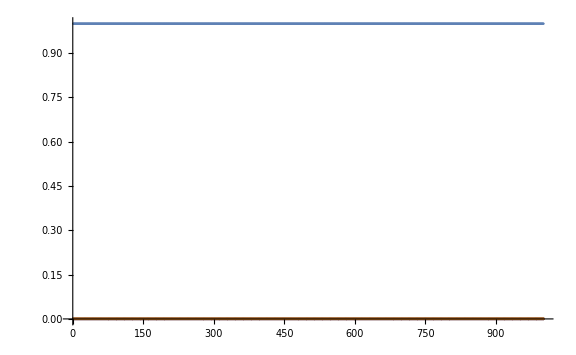

```mathematica
AbsoluteTiming[
resDJ=SolveSchrodinger[HDJ,stateDJ,0,tmaxDJ];
pointsDJ=GetPoints[GetPops[res1],0,tmaxDJ,1000]//Transpose;
]
ListPlot[pointsDJ,ImageSize->Large]
```